```mathematica
Clear["Global`*"];

(*Constants*)
c   =   QuantityMagnitude[Entity["PhysicalConstant","SpeedOfLight"]["Value"]];
e   =   QuantityMagnitude["ElectronCharge","SIBase"]//N;
Subscript[m, e] =   QuantityMagnitude[Entity["PhysicalConstant","ElectronMass"]["Value"]] ;
permittivity =   QuantityMagnitude["VacuumPermittivity","SIBase"]//N;

(*Wavelenght of light creating trapping potential*)
LambdaL = 1064*10^-9;  (*[m], laser wavelength*)
LambdaT =   461*10^-9;  (*[m], atomic transition wavelenght*)

(*Parameters for equations*)
Subscript[w, 0] = 70.71067812*10^-6(*60.0*10^-6/Sqrt[2];         (*m*)*)
power = 100.0;                                 (*W*)
m = 87 1.66054 10^-27;             (*Kg*)
ω   =  N[ c / LambdaL];          (*Hz*)
Subscript[ω, 0] =  N[ c / LambdaT ];         (*Hz*)

(*Rayleigh range*)
zR= (π Subscript[w, 0]^2)/LambdaL;
(*Print["The ratio 2zR^2/w_0^2 = ",2 zR^2/Subscript[w, 0]^2 ]*)

(*Spot size of the beam*)
w[z_] =Sqrt[2]*  Subscript[w, 0] * Sqrt[  1 + (z/zR)^2];

(*Calculating Peak intensity from peak power*)
Subscript[I, 0] = (2 power)/(π Subscript[w, 0]^2);

(*Intensity as a function of position for a gaussian beam*)
Intensity[x_,y_, z_] = Subscript[I, 0] (Subscript[w, 0]/w[z])^2 Exp[(-2*(x^2+ y^2))/w[z]^2];
GradIntensity = Grad[Intensity[x,y,z], {x,y,z}]
Print["the Grad(I(20.0*10^(-6),20.0*10^(-6),20.0*10^(-6))) = "GradIntensity /. {x->20.0*10^(-6),y->20.0*10^(-6),z->20.0*10^(-6)}]

(* Calculating  the  Polerizability *)
Γ = 32*10^6;
α = (3 π c^3 permittivity)/Subscript[ω, 0]^3( Γ/(Subscript[ω, 0]-ω) +Γ/(Subscript[ω, 0]+ω));

(* Potential energy function for a harmonic trap *)
U[x_, y_, z_] = (-1/(2permittivity c))α  Intensity[x,y, z];

(*Calculating trap freq*)
Û= Abs[U[0, 0, 0]];
ωr = Sqrt [4 Û/(m Subscript[w, 0]^2)];
ωz = Sqrt [2 Û/( m  (zR)^2)];
Print ["ωr = ",  ωr]
Print ["ωz = ",  ωz]
Print["The ratio ωr^2/ωz^2 = ",ωr^2/ωz^2 ]

(* Calculating force as a function of posistion *)
Force[x_,y_,z_] = -Grad[U[x,y,z], {x,y,z}]
(*Force[-1*10^(-4), -1*10^(-4), -2*10^(-4)]*)
```

0.0000707107

{-(2.54648×10^18 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) x)/((1+4588.21 z^2)^2),-(2.54648×10^18 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) y)/((1+4588.21 z^2)^2),(1.16838×10^22 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) (x^2+y^2) z)/((1+4588.21 z^2)^3)-(5.84189×10^13 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) z)/((1+4588.21 z^2)^2)}

ωr = 81103.7

ωz = 274.683

The ratio ωr^2/ωz^2 = 87179.9

{-(4.75138×10^-16 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) x)/((1+4588.21 z^2)^2),-(4.75138×10^-16 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) y)/((1+4588.21 z^2)^2),(2.18003×10^-12 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) (x^2+y^2) z)/((1+4588.21 z^2)^3)-(1.09002×10^-20 ⅇ^(-(2.×10^8 (x^2+y^2))/(1+4588.21 z^2)) z)/((1+4588.21 z^2)^2)}

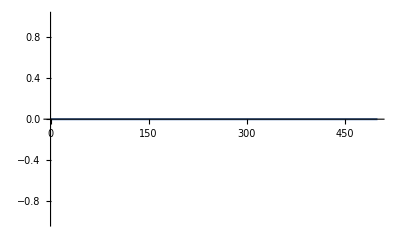

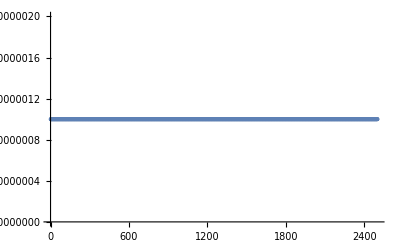

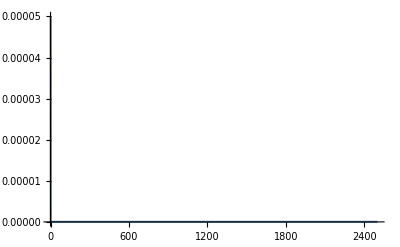

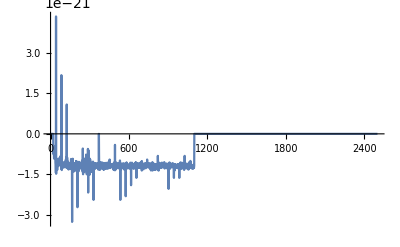

42

```mathematica
Force = Force[f[t],0,0][[1]];
s=NDSolve[{f''[t] + Force==0,f[0]==0.000001, f'[0] == 0},f,{t,0,500}][[1,1,2]];

Plot[s[t],{t,0,500},PlotRange->All]

data00=s/@Range[0,500,1/5];
ListLinePlot[data00,PlotRange->All,PlotStyle->Thick,Joined->False]

data01=Fourier[data00];
ListLinePlot[data01,PlotRange->All]

data03=Table[If[20<i<1100,data01[[i]],0.],{i,Length[data01]}];
ListLinePlot[data03,PlotRange->All]
First[Ordering[data03,-1]]
```

```mathematica
(1000-1)*0.005
```

4.995